```mathematica
dPhi=500;Tm=100;
```

```mathematica
vbth[deltaPhi_,T_]:=√(deltaPhi/T);
```

```mathematica
normFacMaxwellian[T_,kappa_]:=(m/(2 π T))^(3/2)
```

```mathematica
normFacKappa[T_,kappa_]:=(m/(2 π T (1 - 3/(2 kappa))))^(3/2)Gamma[kappa+1]/(kappa^(3/2)Gamma[kappa-1/2])
```

```mathematica
dir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/journals/";
SetDirectory[dir];
<<Liemohn_and_Khazanov__mapped_Maxwellian_density.wl
```

## Distribution functions at source

#### Step function definition

Orig, with potExp

```mathematica
(*pieceFunc[vpar_,vperp_,vbth_,RB_,potExp_]:=Piecewise[{{1,vperp^2(1-RB)+vpar^2+vbth^2(1-RB^-potExp)>0&&vpar>0},{0,vpar≤ 0},{0,vperp^2(1-RB)+vpar^2+vbth^2(1-RB^-potExp)≤ 0}}]*)
```

NotOrig

```mathematica
sourcePieceFuncMax[vpar_,vperp_,vbth_,RB_,potExp_]:=Piecewise[{{1,vperp^2(1-RB)+vpar^2+vbth^2>0&&vpar>0},{0,vpar≤ 0},{0,vperp^2(1-RB)+vpar^2+vbth^2≤ 0}}]
```

#### Maxwellian function definition

Orig Maxwellian

```mathematica
(*funcMaxwellian[vpar_,vperp_,vbth_,RB_,potExp_]:=Exp[-(vpar^2+vperp^2)]UnitStep[vperp^2(1-RB)+vpar^2+vbth^2(1-RB^-potExp)]*)
```

Maxwellian w/ modified step func, in units s.t. v_th=1

```mathematica
sourceFuncMaxwellian[vpar_,vperp_,vbth_,RB_,potExp_]:=1/π^(3/2)Exp[-(vpar^2+vperp^2+vbth^2)]sourcePieceFuncMax[vpar,vperp,vbth,RB,potExp]
```

## Distribution functions at bottom of potential drop

```mathematica
bottomPieceFuncMax[vpar_,vperp_,vbth_,RB_,potExp_]:=Piecewise[{{1,vperp^2(1-1/RB)+vpar^2-vbth^2>0&&vpar>0},{0,vpar≤ 0},{0,vperp^2(1-1/RB)+vpar^2-vbth^2≤ 0}}]
```

```mathematica
bottomPieceFuncMaxRho[rho_,θ_,phiBar_,RB_]:=Piecewise[{{1,rho^2(1- (Sin[θ])^2/RB)-phiBar>0&&rho≥ 0},{0,rho≤ 0},{0,rho^2(1- (Sin[θ])^2/RB)-phiBar< 0}}]
```

```mathematica
bottomFuncMaxwellian[vpar_,vperp_,vbth_,RB_,potExp_]:=1/π^(3/2)Exp[-(vpar^2+vperp^2-vbth^2)]bottomPieceFuncMax[vpar,vperp,vbth,RB,potExp]
```

Cylindrical version that doesn’t seem to work—specifically the order of integration seems to mess up

```mathematica
(*MaxwellGrate[RB_,phiBar_]:=2/(√π)NIntegrate[rho^2 Sin[theta] Exp[-rho^2+phiBar],{theta,0,π/2},{rho,phiBar/(1-(Sin[theta])^2/RB),20}]*)
```

Cylindrical version that does work (or at least matches the analytical expression)

```mathematica
MaxwellGrate[RB_,phiBar_]:=2/(√π)NIntegrate[rho^2 Sin[theta] Exp[-rho^2+phiBar]bottomPieceFuncMaxRho[rho,theta,phiBar,RB],{theta,0,π/2},{rho,0,20}]
```

## Now for some plots!

#### Function at source, with lines showing which particles make it to the bottom (I think)

```mathematica
Manipulate[Plot3D[sourceFuncMaxwellian[vpar,vperp,vbth,RB,1],{vpar,0,5},{vperp,-2.5,2.5},PlotRange->Full,ImageSize->700],{RB,{1,3/2,2,5/2,3,10,30,50,70,100,200,300,500,700,1000}},{vbth,0,20}]
```

```mathematica
RB=1
```

```mathematica
vbth1=0;
```

```mathematica
vbth2=Sqrt@5;
```

```mathematica
Plot3D[{Log10@sourceFuncMaxwellian[vpar,vperp,vbth1,RB,1],Log10@sourceFuncMaxwellian[vpar,vperp,vbth2,RB,1]},{vpar,0,5},{vperp,-2.5,2.5},PlotRange->{Full,Full,{-5,-0.7}},PlotStyle->{{Blue,Opacity[0.5]},{Yellow,Opacity[0.2]}},Mesh->5,ImageSize->700]
```

-Graphics3D-

#### Function at bottom of potential drop (for dPhi=941 V, T_m=110 eV)

```mathematica
Manipulate[Plot3D[bottomFuncMaxwellian[vpar,vperp,vbth,RB,1],{vpar,0,5},{vperp,0,5},PlotRange->Full,AxesLabel->Automatic,ImageSize->600],{{RB,72},{1,3/2,2,5/2,3,10,30,50,70,100,200,300,500,700,1000}},{{vbth,√(dPhi/Tm)},0,4}]
```

#### Use rho representation

```mathematica
ParametricPlot3D[{rho Cos[theta],rho Sin[theta],Exp[-rho^2+dPhi/Tm] bottomPieceFuncMaxRho[rho,theta,dPhi/Tm,80]},{rho,0,6},{theta,0,π/2},PlotRange->All]
```

-Graphics3D-

```mathematica
Manipulate[ContourPlot[bottomFuncMaxwellian[vpar,vperp,vbth,RB,1],{vpar,0,5},{vperp,0,5},PlotRange->Full,FrameLabel->{"vPar","vPerp"},ImageSize->600],{{RB,1},{1,3/2,2,5/2,3,10,30,50,70,100,200,300,500,700,1000}},{{vbth,√(dPhi/Tm)},0,4}]
```

## Jim wanted to know why the density is so low for R_B=1. Here’s the answer:

#### First, a plot (for dPhi=941 V, T_m=110 eV):

```mathematica
Manipulate[Plot3D[bottomFuncMaxwellian[vpar,vperp,vbth,RB,1],{vpar,0,5},{vperp,0,5},PlotRange->Full,AxesLabel->Automatic,ImageSize->600],{{RB,1},{1,3/2,2,5/2,3,10,30,50,70,100,200,300,500,700,1000}},{{vbth,√(dPhi/Tm)},0,4}]
```

#### Now, a NIntegrate over the corresponding region:

```mathematica
NIntegrate[2 π vperp bottomFuncMaxwellian[vpar,vperp,vbth[dPhi,Tm],1,1],{vpar,vbth[dPhi,Tm],5},{vperp,0,5}]
```

0.0915904

#### Compare with my analytic expression:

```mathematica
LKMwellDensFac[dPhi/Tm,1.000000001]
```

0.0915904

#### Exactly! So that’s it—very low density. But how about a full curve?

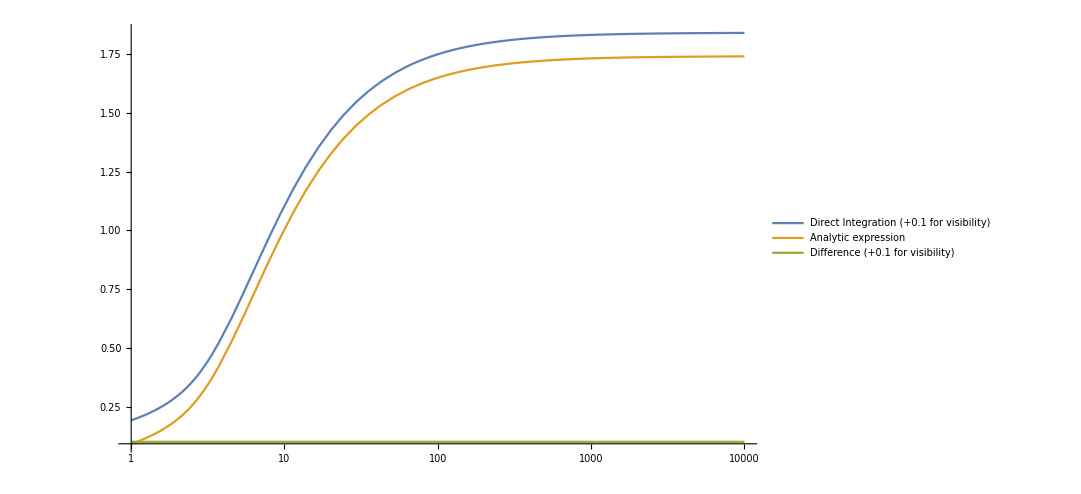

```mathematica
LogLinearPlot[{NIntegrate[2 π vperp bottomFuncMaxwellian[vpar,vperp,vbth[dPhi,Tm],RB,1],{vpar,0,5},{vperp,0,5}]+0.1,LKMwellDensFac[dPhi/Tm,RB],NIntegrate[2 π vperp bottomFuncMaxwellian[vpar,vperp,vbth[dPhi,Tm],RB,1],{vpar,0,5},{vperp,0,5}]+0.1-LKMwellDensFac[dPhi/Tm,RB]},{RB,1,10000},PlotRange->All,PlotLegends->{"Direct Integration (+0.1 for visibility)","Analytic expression","Difference (+0.1 for visibility)"},ImageSize->800]
```

```mathematica
NIntegrate[2 π vperp bottomFuncMaxwellian[vpar,vperp,vbth[dPhi,Tm],10,1],{vpar,0,5},{vperp,0,5}]
```

1.00506

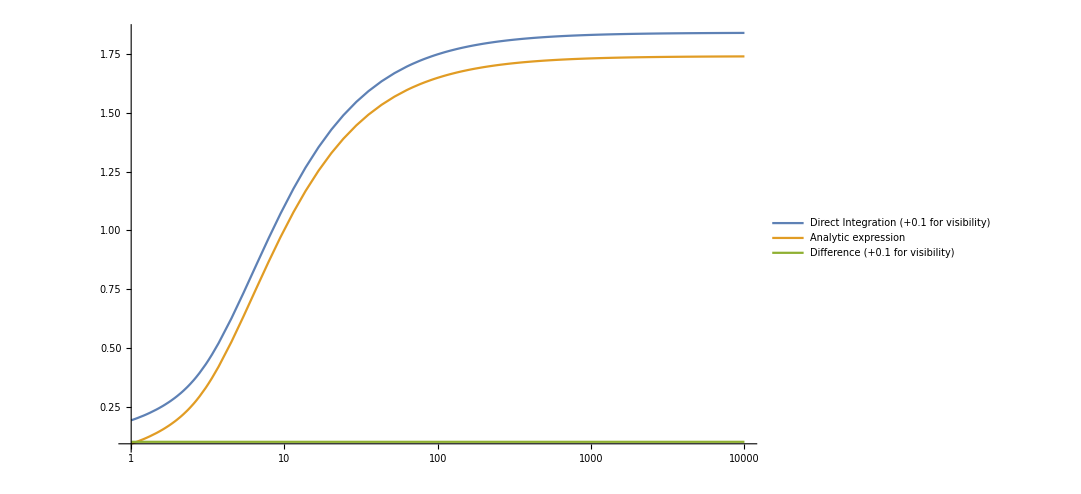

```mathematica
LogLinearPlot[{MaxwellGrate[RB,dPhi/Tm]+0.1,LKMwellDensFac[dPhi/Tm,RB],MaxwellGrate[RB,dPhi/Tm]+0.1-LKMwellDensFac[dPhi/Tm,RB]},{RB,1,10000},PlotRange->All,PlotLegends->{"Direct Integration (+0.1 for visibility)","Analytic expression","Difference (+0.1 for visibility)"},ImageSize->800]
```

```mathematica
Table[{{MaxwellGrate[RB,dPhi/Tm],LKMwellDensFac[dPhi/Tm,RB]//N}},{RB,{101/100,10,100,1000,10000}}]
```

{{{0.0925555,0.0925555}},{{1.00506,1.00506}},{{1.64989,1.64989}},{{1.73235,1.73235}},{{1.7408,1.7408}}}